### Simplex Plot

```mathematica
(* Geometric transformation to simplex *)
{err,trans}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
(* Edges of simplex *)
triangle=Graphics[{Thickness[0.005],Darker[Gray],GeometricTransformation[Line[{{0,0},{0,1},{1,0},{0,0}}],trans]}];
(* Some random data *)
dummyData=Select[RandomReal[1,{100,2}],Total[#]<=1&];
(* Plot the points *)
points=ListPlot[dummyData,PlotStyle->PointSize[0.03]];
(* Or plot the lines *)
lines=ListLinePlot[dummyData,PlotStyle->Black];
(* Show all together *)
(* The trick is to extract the "First" part of the plots, and transform it *)
```

```mathematica
TA=({{-1/2, -1}, {(√3)/2, 0}})  ;
(* new maps points in the simplex to their 2D representation for graphing, old does the reverse *)
new[r_]:=TA.{r⟦1⟧,r⟦2⟧}+{1,0} ;
old2[c_]:=Inverse[TA].(c-{1,0}) ;
old[c_]:={old2[c]⟦1⟧,old2[c]⟦2⟧,1-old2[c]⟦1⟧-old2[c]⟦2⟧} ;
```

## Data processing

```mathematica
SetDirectory[NotebookDirectory[]<>"simulation_data/"]
```

/Users/chaitanyagokhale/Documents/Working/Srishti/Overleafdata/matecopying_multiplemorphs/fig3_new/simulation_data

```mathematica
filenames=FileNames[];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/chaitanyagokhale/Documents/Working/Srishti/Overleafdata/matecopying_multiplemorphs/fig3_new

```mathematica
filenames
```

{3m_c0.0.csv,3m_c0.10.csv,3m_c0.15.csv,3m_c0.20.csv,3m_c0.25.csv,3m_c0.30.csv,3m_c0.35.csv,3m_c0.40.csv,3m_c0.45.csv,3m_c0.50.csv,3m_c0.55.csv,3m_c0.60.csv,3m_c0.65.csv,3m_c0.70.csv,3m_c0.75.csv,3m_c0.80.csv,3m_c0.85.csv,3m_c0.90.csv,3m_c0.95.csv,3m_c1.0.csv}

```mathematica
raw3mdata=Table[Import[NotebookDirectory[]<>"simulation_data/"<>ToString[filenames⟦i⟧],"CSV"],{i,1,Length[filenames],1}];
```

```mathematica
raw3mdata//Dimensions
```

{20,1275,3}

```mathematica
file1=.;
```

```mathematica
transformedlist=Table[Join[new[#⟦1;;2⟧],{#⟦3⟧}]&/@raw3mdata⟦i,2;;⟧,{i,1,20,1}];
```

```mathematica
Manipulate[Show[ListDensityPlot[transformedlist⟦i⟧,InterpolationOrder->3,ColorFunction->"SouthwestColors",PlotLegends->Automatic,PlotLayout->{"Row", 2},Frame->False,PlotRange->All,Epilog->Inset[Graphics[Text[ToString[filenames⟦i⟧]]],{0.2,0.7}]],triangle],{i,1,20,1}]
```

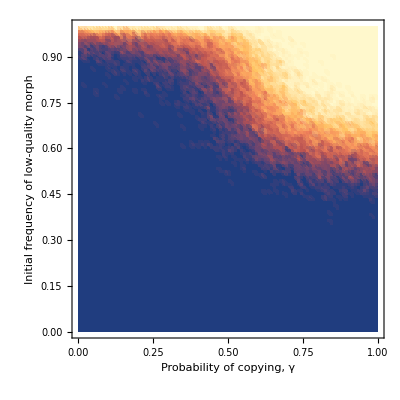

```mathematica
ListDensityPlot[rawfig2a⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}]
```

```mathematica
rawfig2b=Import[NotebookDirectory[]<>"fig2b_data.csv","CSV"];
```

```mathematica
rawfig2b⟦2;;10⟧
```

{{0.,0.,0.},{0.,0.01,0.0005},{0.,0.02,0.004},{0.,0.03,0.006},{0.,0.04,0.0075},{0.,0.05,0.0085},{0.,0.06,0.0095},{0.,0.07,0.0105},{0.,0.08,0.011}}

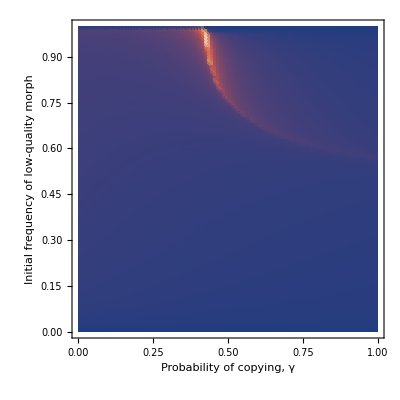

```mathematica
ListDensityPlot[rawfig2b⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Normalised fixation time",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}]
```

```mathematica
rawfig2c=Import[NotebookDirectory[]<>"fig2c_data.csv","CSV"];
```

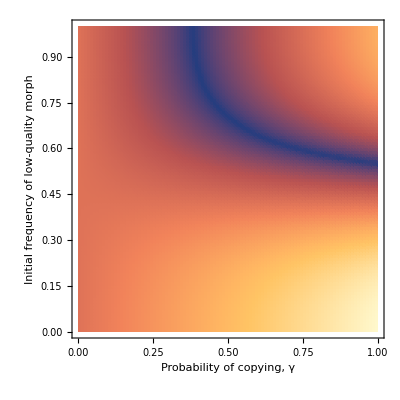

```mathematica
ListDensityPlot[rawfig2c⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Absolute difference in modified qualities",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]}]
```